```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["OG_Josh_o1through4.m"]
```

```mathematica
For[k = 0, k ≤4,k++,
Josh[k] = Exp[γ  (y  - x)]* Sum[(-1/2)^j (γ)^(2j) * o[j], {j, 0, k}]
]
```

```mathematica
Clear[o]
```

```mathematica
GaussianApprox= (2 π x (1-x) t)^(-1/2) Exp[-(y-(x+2Ne α Λ x (1-x) t / W))^2 / (2 x (1-x) t)]
```

(ⅇ^(-(-x+y-(2 Ne t (1-x) x α Λ)/W)^2/(2 t (1-x) x)))/(√(2 π) √(t (1-x) x))

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,10];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.00101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe,α->0.01},
g,{x,0,1},MaxStepSize->.000025]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

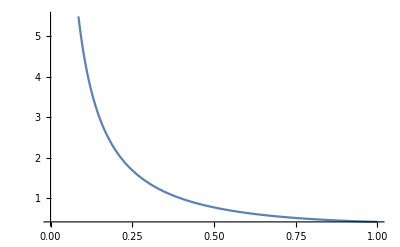

```mathematica
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
```

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.52598}

```mathematica
pNeutFix = 1- neutAUC
```

```mathematica
tmp = NIntegrate[Evaluate[neutral /. {x->start, t->time}]* Evaluate[g[x] /(equilAUC x(1-x))/. x->start /.blah],{y, Max[0,start-Ψ], Min[1,start+Ψ]}, {start,0,1}]
```

NIntegrate::nlim: y = Max[0,start-Ψ] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{NIntegrate[1/((1-start) start)0.180963 (4.6728 (1-start) start+0.520637 (-3/2+15/2 (1-2 start)^2) (1-start) start (-3/2+15/2 (1-2 y)^2)+0.147753 (-15/2 (1-2 start)+35/2 (1-2 start)^3) (1-start) start (-15/2 (1-2 y)+35/2 (1-2 y)^3)+0.0344927 (15/8-105/4 (1-2 start)^2+315/8 (1-2 start)^4) (1-start) start (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4)+0.00649693 (105/8 (1-2 start)-315/4 (1-2 start)^3+693/8 (1-2 start)^5) (1-start) start (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)+0.000977016 (-35/16+945/16 (1-2 start)^2-3465/16 (1-2 start)^4+3003/16 (1-2 start)^6) (1-start) start (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+0.000116554 (-315/16 (1-2 start)+3465/16 (1-2 start)^3-9009/16 (1-2 start)^5+6435/16 (1-2 start)^7) (1-start) start (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+0.0000109839 (315/128-3465/32 (1-2 start)^2+45045/64 (1-2 start)^4-45045/32 (1-2 start)^6+109395/128 (1-2 start)^8) (1-start) start (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+8.15338×10^-7 (3465/128 (1-2 start)-15015/32 (1-2 start)^3+135135/64 (1-2 start)^5-109395/32 (1-2 start)^7+230945/128 (1-2 start)^9) (1-start) start (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+14.171 (1-2 start) (1-start) start (1-2 y)) InterpolatingFunction[{{0., 1.}}, <>][start],{y,Max[0,start-Ψ],Min[1,start+Ψ]},{start,0,1}]}}